## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PRAli";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/home/kevin/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_trp3_milos.csv";

mainFolder = "fit_PRAli_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/home/kevin/Desktop/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

(pran^c⇌(2cpr5p)^c)^PRAli

Uni-uni;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pran | Null | 10.3 | 9.785
10.815 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pran | 4.7×10^-6 | 4.465×10^-6
4.935×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.7×10^-6 | 4.465×10^-6
4.935×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.9×10^-6 | 4.655×10^-6
5.145×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.9×10^-6 | 4.655×10^-6
5.145×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.9×10^-6 | 4.655×10^-6
5.145×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 7.×10^-6 | 6.65×10^-6
7.35×10^-6 |  | M | 7.5 | 20 | trisac | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pran | Null | 96.09 | 91.2855
100.894 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 96.09 | 91.2855
100.894 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 185.167 | 175.908
194.425 | 1/s | 7.5 | 37 | trisac | 0.1 | 
1 | pran | Null | 120.112 | 114.107
126.118 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 120.112 | 114.107
126.118 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 5. | 4.75
5.25 | 1/s | 7.5 | 37 |  | 
1 | pran | Null | 120.112 | 114.107
126.118 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | Reduced1-(2-carboxyphenylamino)-1-deoxy-D-ribulose5-phosphate | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 |  |  | M | 7.5 | 25 |  | 
1 | Ki | Reduced1-(2-carboxyphenylamino)-1-deoxy-D-ribulose5-phosphate | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 |  |  | M | 7.5 | 25 |  | 
1 | Ki | Reduced1-(2-carboxyphenylamino)-1-deoxy-D-ribulose5-phosphate | 6.8×10^-6 | 6.46×10^-6
7.14×10^-6 |  |  | M |  | 25 |  | 
1 | Kic | 2cpr5p | 6.8×10^-6 | 6.46×10^-6
7.14×10^-6 |  | Competitive | pran | 4.9×10^-6 | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | 
1 | Ki | Reduced1-(2-carboxyphenylamino)-1-deoxy-D-ribulose5-phosphate | 6.8×10^-6 | 6.46×10^-6
7.14×10^-6 |  |  | M | 7.5 | 25 |  |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1,1,1,1,1,1};
inhibitionPriorities={0,0,0,1,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(pran^c⇌(2cpr5p)^c)^PRAli

Uni-uni;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pran | Null | 10.3 | 9.785
10.815 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pran | 4.7×10^-6 | 4.465×10^-6
4.935×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.7×10^-6 | 4.465×10^-6
4.935×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.9×10^-6 | 4.655×10^-6
5.145×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.9×10^-6 | 4.655×10^-6
5.145×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 4.9×10^-6 | 4.655×10^-6
5.145×10^-6 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | 7.×10^-6 | 6.65×10^-6
7.35×10^-6 |  | M | 7.5 | 20 | trisac | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pran | Null | 96.09 | 91.2855
100.894 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 96.09 | 91.2855
100.894 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 185.167 | 175.908
194.425 | 1/s | 7.5 | 37 | trisac | 0.1 | 
1 | pran | Null | 120.112 | 114.107
126.118 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 120.112 | 114.107
126.118 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | pran | Null | 5. | 4.75
5.25 | 1/s | 7.5 | 37 |  | 
1 | pran | Null | 120.112 | 114.107
126.118 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | 2cpr5p | 6.8×10^-6 | 6.46×10^-6
7.14×10^-6 |  | Competitive | pran | 4.9×10^-6 | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PRAli[c] + pran[c] <=> E_PRAli[c]&pran",
				"E_PRAli[c]&pran <=> E_PRAli[c]&2cpr5p",
				"E_PRAli[c]&2cpr5p <=> E_PRAli[c] + 2cpr5p[c]"};



enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PRAli^c)_^+pran^c⇌(PRAli^c&pran^c)_^)^PRAli1,((PRAli^c&(2cpr5p)^c)_^⇌(PRAli^c)_^+(2cpr5p)^c)^PRAli2,((PRAli^c&pran^c)_^⇌(PRAli^c&(2cpr5p)^c)_^)^PRAli3}

```mathematica
Print[enzymeModel]
```

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PRAli^c)_^+pran^c⇌(PRAli^c&pran^c)_^)^PRAli1,Overscript[(PRAli^c&(2cpr5p)^c)_^⇌(PRAli^c)_^+(2cpr5p)^c, PRAli2],((PRAli^c&pran^c)_^⇌(PRAli^c&(2cpr5p)^c)_^)^PRAli3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={"prod_inhib_2cpr5p", metabolite["2cpr5p", "c"]->0};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

prod inhib

Generating flux equation...

{((PRAli^c&pran^c)_^-((PRAli^c&(2cpr5p)^c)_^)/K_PRAli3) Volume_c k_PRAli3^⟶}

Volume_c (-(PRAli^c&(2cpr5p)^c)_^ k_PRAli3^⟵+(PRAli^c&pran^c)_^ k_PRAli3^⟶)

Simplifying...

Added inhibition reactions:

{((PRAli^c)_^+(2cpr5p)^c⇌(PRAli^c&(2cpr5p)^c)_^)^PRAli_Kic_2cpr5p_1_pran}

Generating flux equation...

{((PRAli^c&pran^c)_^-((PRAli^c&(2cpr5p)^c)_^)/K_PRAli3) Volume_c k_PRAli3^⟶}

Volume_c (-(PRAli^c&(2cpr5p)^c)_^ k_PRAli3^⟵+(PRAli^c&pran^c)_^ k_PRAli3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate reverse equation...

Simplifying...

Part::partd: Part specification prod_inhib_2cpr5p⟦1⟧ is longer than depth of object.

StringJoin::string: String expected at position 2 in otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧.

Part::partd: Part specification prod_inhib_2cpr5p⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {prod_inhib_2cpr5p⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringJoin::string: String expected at position 2 in otherRateRelRev_2cpr5p_<>(2cpr5p)^c.

ReplaceAll::reps: {0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

StringJoin::string: String expected at position 2 in otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Export::chtype: First argument FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt},OperatingSystem→Unix] is not a valid file specification.

Export::chtype: First argument FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>(2cpr5p)^c<>.txt},OperatingSystem→Unix] is not a valid file specification.

```mathematica
Print[enzymeModel]
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt},OperatingSystem→Unix],RegularExpression[.*relRate.*_pran\.txt]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>(2cpr5p)^c<>.txt},OperatingSystem→Unix],RegularExpression[.*relRate.*_pran\.txt]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt},OperatingSystem→Unix],RegularExpression[.*relRate.*_pran\.txt]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Simulating kcat data...

Simulating inhibition data...

StringCases::strse: String or list of strings expected at position 1 in StringCases[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt,/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/absRateRev.txt,/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt,/home/kevin/Deskt…RateRev_2cpr5p.txt,FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt},OperatingSystem→Unix],FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>(2cpr5p)^c<>.txt},OperatingSystem→Unix],/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt},«1»].

StringJoin::string: String expected at position 2 in "/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/absRateRev.txt/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/relRateRev_2cpr5p.txt<>FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt},OperatingSystem→Unix]<>FileNameJoin[«1»,OperatingSystem→Unix]<>/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt".

StringJoin::string: String expected at position 3 in "/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/absRateRev.txt/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/relRateRev_2cpr5p.txt<>FileNameJoin[{/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input,otherRateRelRev_2cpr5p_<>prod_inhib_2cpr5p⟦1⟧<>.txt},OperatingSystem→Unix]<>FileNameJoin[«1»,OperatingSystem→Unix]<>/home/kevin/Desktop/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt".

```mathematica
Print[bufferInfo]
```

{{{trishcl,Tris-HCl},8.14,1,0},{{tris,Tris},8.14,1,0},{{trisac,Tris-acetate},8.14,1,0},{{edta,EDTA},Null,Null,Null},{{tric,Tricine},8.07,0,-1},{{tricna,Tricine-Na},8.07,0,-1},{{hepesnaoh,Hepes-NaOH},7.5,0,-1},{{pipeskoh,PIPES-KOH},6.64,-1,-2},{{kpi,KPO4},6.88,-1,-2},{{napi,sodium phosphate},6.88,-1,-2},{{nakpi,Na+/K+ phosphate},6.88,-1,-2},{{chesk,CHES-K},9.37,0,-1},{{hepes,Hepes},7.5,0,-1},{{hepesbtp,HEPES-BTP},Null,Null,Null},{{pipes,Pipes},6.64,-1,-2},{{mops,MOPS},7.12,0,-1},{{mopsnaoh,MOPS/NaOH},7.12,0,-1},{{mopskoh,MOPS-KOH},7.12,0,-1},{{mes,MES},6.14,0,-1},{{netmphn,N-ethylmorpholine},7.83,1,0},{{detam,diethanolamine},8.95,1,0},{{glygly,glycylglycine},8.2,0,-1},{{imdzcl,imidazole-Cl},7.06,1,0},{{imdz_MIXED,mixed imidazoles},Null,Null,Null},{{24dmid,2,4-dimethylimidazole},Null,Null,Null},{{teoa,triethanolamine},7.83,1,0},{{teoahcl,triethanolamine-HCl},7.83,1,0},{{pi_buffer,Phosphoric acid},7.198,-1,-2},{{dtpa,DTPA},Null,Null,Null}}

```mathematica
FilePrint@dataPathList
```

Priority	2cpr5p[c]	pran[c]	param_PRAli_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt"	10.3
1	0	4.699999999999996e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.09090909090909084
1	0	7.44899800456723e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.13680688860320994
1	0	1.1805866228095025e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.20076000891310175
1	0	1.8711037016014378e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.2847472489508015
1	0	2.9654995190569044e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.38686317984685664
1	0	4.699999999999996e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.49999999999999983
1	0	7.44899800456723e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.613136820153143
1	0	0.000011805866228095026	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7152527510491986
1	0	0.000018711037016014376	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7992399910868984
1	0	0.000029654995190569043	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.8631931113967898
1	0	0.000046999999999999957	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.9090909090909091
1	0	4.699999999999996e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.09090909090909084
1	0	7.44899800456723e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.13680688860320994
1	0	1.1805866228095025e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.20076000891310175
1	0	1.8711037016014378e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.2847472489508015
1	0	2.9654995190569044e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.38686317984685664
1	0	4.699999999999996e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.49999999999999983
1	0	7.44899800456723e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.613136820153143
1	0	0.000011805866228095026	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7152527510491986
1	0	0.000018711037016014376	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7992399910868984
1	0	0.000029654995190569043	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.8631931113967898
1	0	0.000046999999999999957	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.9090909090909091
1	0	4.900000000000002e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.09090909090909094
1	0	7.765976643059463e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.1368068886032101
1	0	1.2308243514396957e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.20076000891310194
1	0	1.9507251357121358e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.28474724895080133
1	0	3.091690987952947e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.3868631798468569
1	0	4.900000000000002e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.5000000000000002
1	0	7.765976643059462e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.6131368201531433
1	0	0.000012308243514396957	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7152527510491988
1	0	0.000019507251357121357	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7992399910868981
1	0	0.00003091690987952947	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.8631931113967901
1	0	0.00004900000000000002	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.9090909090909092
1	0	4.900000000000002e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.09090909090909094
1	0	7.765976643059463e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.1368068886032101
1	0	1.2308243514396957e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.20076000891310194
1	0	1.9507251357121358e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.28474724895080133
1	0	3.091690987952947e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.3868631798468569
1	0	4.900000000000002e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.5000000000000002
1	0	7.765976643059462e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.6131368201531433
1	0	0.000012308243514396957	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7152527510491988
1	0	0.000019507251357121357	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7992399910868981
1	0	0.00003091690987952947	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.8631931113967901
1	0	0.00004900000000000002	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.9090909090909092
1	0	4.900000000000002e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.09090909090909094
1	0	7.765976643059463e-7	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.1368068886032101
1	0	1.2308243514396957e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.20076000891310194
1	0	1.9507251357121358e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.28474724895080133
1	0	3.091690987952947e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.3868631798468569
1	0	4.900000000000002e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.5000000000000002
1	0	7.765976643059462e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.6131368201531433
1	0	0.000012308243514396957	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7152527510491988
1	0	0.000019507251357121357	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7992399910868981
1	0	0.00003091690987952947	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.8631931113967901
1	0	0.00004900000000000002	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.9090909090909092
1	0	7.000000000000002e-7	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.09090909090909093
1	0	1.1094252347227802e-6	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.13680688860321008
1	0	1.7583205020567078e-6	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.20076000891310192
1	0	2.786750193874479e-6	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.2847472489508013
1	0	4.416701411361352e-6	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.38686317984685686
1	0	7.000000000000002e-6	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.5
1	0	0.000011094252347227801	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.6131368201531432
1	0	0.00001758320502056708	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7152527510491987
1	0	0.000027867501938744792	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.7992399910868982
1	0	0.000044167014113613516	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.8631931113967899
1	0	0.00007000000000000002	1	7.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt"	0.9090909090909092
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	96.08995471851452
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	185.16658702726616
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314
1	0	0.01	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt"	120.11244339814314

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Set::shape: Lists {allFittingDataList,dataPathList,fileList,fileListSub} and RowBox[{"simulateDataWithUncertainty", "[", RowBox[{"10", ",", TagBox[DynamicModuleBox[{Typeset`var$$ = 1}, InterpretationBox[TagBox[PanelBox[GridBox[{{ItemBox[PopupMenuBox[Dynamic[Typeset`var$$], {1 -> "\"Overview\"", 2 -> "\"Stoichiometry matrix\"", 3 -> "\"Reactions\"", 4 -> "\"Rates\"", 5 -> "\"ODE\"", 6 -> "\"Constraints\"", 7 -> "\"Initial conditions\"", 8 -> "\"Parameters\"", 9 -> "\"GPR\"", 10 -> "\"Pathway map\"", 11 -> "\"Nullspace\"", 12 -> "\"Left Nullspace\"", 13 -> "\"Notes\"", 14 -> "\"Preset Pathways\""}, Enabled -> Automatic, MenuStyle -> {}, DefaultMenuStyle -> "MenuViewLabel"], Alignment -> Left, StripOnInput -> False]}, {ItemBox[StyleBox[PaneSelectorBox[{1 -> PaneBox[StyleBox[TagBox[GridBox[{{"\"Number of species(rows):\"", "5"}, {"\"Number of columns(reactions):\"", "3"}, {"\"Number of exchange reactions:\"", "0"}, {"\"Number of irreversible reactions:\"", "0"}, {"\"Matrix rank:\"", "3"}, {"\"Dimensions null space: \"", "0"}, {"\"Dimensions left null space: \"", "2"}, {"\"Number of parameters\"", "1"}, {"\"Number of custom rate equations\"", "0"}, {"\"Number of equilibrium constants:\"", "0"}, {"\"Number of forward rate constants:\"", "0"}, {"\"Number of initial concentrations:\"", "0"}, {"\"Number of genes:\"", "0"}, {"\"Number of proteins:\"", "0"}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 2 -> TemplateBox[{GraphicsBox[RasterBox[{{{1., 1., 1.}, {1., 0., 0.}, {0., 1., 0.}}, {{1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}}, {{1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}}, {{0., 1., 0.}, {1., 1., 1.}, {1., 0., 0.}}, {{1., 0., 0.}, {0., 1., 0.}, {1., 1., 1.}}}, {{0, 0}, {3, 5}}, {0, 1}], BaseStyle -> {FontFamily -> "Helvetica", FontSize -> Scaled[0.015]}, Frame -> True, FrameLabel -> {None, None}, FrameTicks -> {{{{4.5, FormBox["1", TraditionalForm]}, {3.5, FormBox["2", TraditionalForm]}, {2.5, FormBox["3", TraditionalForm]}, {1.5, FormBox["4", TraditionalForm]}, {0.5, FormBox["5", TraditionalForm]}}, {{4.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {3.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {2.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]], Annotation[#1, ru5p__D^c, "Tooltip"] & ], TraditionalForm]}, {1.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]], Annotation[#1, xu5p__D^c, "Tooltip"] & ], TraditionalForm]}, {0.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}}}, {{{0.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"RPE1\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {1.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"RPE2\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {2.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"RPE3\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}}, {{0.5, FormBox["1", TraditionalForm]}, {1.5, FormBox["2", TraditionalForm]}, {2.5, FormBox["3", TraditionalForm]}}}}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], ImageSize -> {{800}, {450}}, Method -> {"AxisPadding" -> Scaled[0.02], "DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, "DefaultPlotStyle" -> Automatic, "DomainPadding" -> Scaled[0.02], "RangePadding" -> Scaled[0.05]}], FormBox[FormBox[TemplateBox[{"\"\\!\\(\\*SubscriptBox[\\(S\\), \\(i, j\\)]\\) = 0\"", "\"\\!\\(\\*SubscriptBox[\\(S\\), \\(\\(i\\)\\(,\\)\\(j\\)\\(\\\\ \\)\\)]\\)> 0\"", "\"\\!\\(\\*SubscriptBox[\\(S\\), \\(\\(i\\)\\(,\\)\\(j\\)\\(\\\\ \\)\\)]\\)< 0\""}, "SwatchLegend", DisplayFunction -> (FormBox[StyleBox[StyleBox[PaneBox[TagBox[GridBox[{{TagBox[GridBox[{{GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], GrayLevel[1]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #1}, {GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], RGBColor[0, 1, 0]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #2}, {GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], RGBColor[1, 0, 0]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #3}}, GridBoxAlignment -> {"Columns" -> {Center, Left}, "Rows" -> {{Baseline}}}, AutoDelete -> False, GridBoxDividers -> {"Columns" -> {{False}}, "Rows" -> {{False}}}, GridBoxItemSize -> {"Columns" -> {{All}}, "Rows" -> {{All}}}, GridBoxSpacings -> {"Columns" -> {{0.5}}, "Rows" -> {{0.5}}}], "Grid"]}}, GridBoxAlignment -> {"Columns" -> {{Left}}, "Rows" -> {{Top}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{0}}}], "Grid"], Alignment -> Left, AppearanceElements -> None, ImageMargins -> {{5, 5}, {5, 5}}, ImageSizeAction -> "ResizeToFit"], LineIndent -> 0, StripOnInput -> False], {FontFamily -> "Arial"}, Background -> Automatic, StripOnInput -> False], TraditionalForm] & ), InterpretationFunction :> (RowBox[{"SwatchLegend", "[", RowBox[{RowBox[{"{", RowBox[{InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {GrayLevel[1], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> GrayLevel[0.6666666666666666], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"GrayLevel", "[", "1", "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = GrayLevel[1]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["GrayLevelColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], GrayLevel[1], Editable -> False, Selectable -> False], ",", InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[0, 1, 0], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> RGBColor[0., 0.6666666666666666, 0.], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"RGBColor", "[", RowBox[{"0", ",", "1", ",", "0"}], "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[0, 1, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], RGBColor[0, 1, 0], Editable -> False, Selectable -> False], ",", InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[1, 0, 0], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> RGBColor[0.6666666666666666, 0., 0.], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"RGBColor", "[", RowBox[{"1", ",", "0", ",", "0"}], "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[1, 0, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], RGBColor[1, 0, 0], Editable -> False, Selectable -> False]}], "}"}], ",", RowBox[{"{", RowBox[{#1, ",", #2, ",", #3}], "}"}]}], "]"}] & ), Editable -> True], TraditionalForm], TraditionalForm]}, "Legended", DisplayFunction -> (GridBox[{{TagBox[ItemBox[PaneBox[TagBox[#1, "SkipImageSizeLevel"], Alignment -> {Center, Baseline}, BaselinePosition -> Baseline], DefaultBaseStyle -> "Labeled"], "SkipImageSizeLevel"], ItemBox[#2, DefaultBaseStyle -> "LabeledLabel"]}}, GridBoxAlignment -> {"Columns" -> {{Center}}, "Rows" -> {{Center}}}, AutoDelete -> False, GridBoxItemSize -> Automatic, BaselinePosition -> {1, 1}] & ), InterpretationFunction -> (RowBox[{"Legended", "[", RowBox[{#1, ",", RowBox[{"Placed", "[", RowBox[{#2, ",", "After"}], "]"}]}], "]"}] & ), Editable -> True], 3 -> PaneBox[StyleBox[TagBox[GridBox[{{InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, GridBoxBackground -> {"Columns" -> {{Automatic}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, DefaultBaseStyle -> "Column", GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Column"], FontSize -> 12, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 4 -> PaneBox[TabViewBox[{{1, "\"Type I\"" -> StyleBox[TagBox[GridBox[{{InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE1"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE2"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE3"], Selectable -> False, Editable -> False], RowBox[{RowBox[{"-", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]]}], ")"}]}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}]}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False]}, {2, "\"Type II\"" -> StyleBox[TagBox[GridBox[{{InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE1"], Selectable -> False, Editable -> False], RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE1", False], Selectable -> False, Editable -> False]}], "+", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE2"], Selectable -> False, Editable -> False], RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], "-", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE2", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE3"], Selectable -> False, Editable -> False], RowBox[{RowBox[{"-", RowBox[{"(", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE3", False], Selectable -> False, Editable -> False], "-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False]}], ")"}]}], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}]}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False]}, {3, "\"Type III\"" -> StyleBox[TagBox[GridBox[{{InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE1"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE1", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", RowBox[{InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE2"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE2", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False], "-", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE3"], Selectable -> False, Editable -> False], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]}], ")"}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE3", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}]}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False]}}, 1], Scrollbars -> {False, True}, ImageSize -> {{800}, {450}}], 5 -> PaneBox[StyleBox[TagBox[GridBox[{{RowBox[{RowBox[{RowBox[{"parameter", "[", RowBox[{"\"Volume\"", ",", RowBox[{"\"Compartment\"", "/.", "", RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]}]}], "]"}], " ", RowBox[{SuperscriptBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{RowBox[{"-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False]}], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}], "+", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}]}]}, {RowBox[{RowBox[{RowBox[{"parameter", "[", RowBox[{"\"Volume\"", ",", RowBox[{"\"Compartment\"", "/.", "", RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]}]}], "]"}], " ", RowBox[{SuperscriptBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]]}], ")"}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}], "+", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}]}]}, {RowBox[{RowBox[{InterpretationBox[UnderscriptBox[StyleBox["Volume", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], parameter["Volume", "c"], Selectable -> False, Editable -> False], " ", RowBox[{SuperscriptBox[RowBox[{"(", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], ")"}], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{"-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False]}], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}]}, {RowBox[{RowBox[{InterpretationBox[UnderscriptBox[StyleBox["Volume", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], parameter["Volume", "c"], Selectable -> False, Editable -> False], " ", RowBox[{SuperscriptBox[RowBox[{"(", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], ")"}], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}]}, {RowBox[{RowBox[{RowBox[{"parameter", "[", RowBox[{"\"Volume\"", ",", RowBox[{"\"Compartment\"", "/.", "", RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]}]}], "]"}], " ", RowBox[{SuperscriptBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{RowBox[{"-", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]]}], ")"}]}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}], "-", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}]}]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, GridBoxBackground -> {"Columns" -> {{Automatic}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, DefaultBaseStyle -> "Column", GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Column"], FontSize -> 10, StripOnInput -> False], Scrollbars -> {False, True}, ImageSize -> {{800}, {450}}], 6 -> PaneBox[StyleBox[TagBox[RowBox[{"{", "}"}], Function[BoxForm`e$, TableForm[BoxForm`e$]]], FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 7 -> PaneBox[StyleBox[TagBox[RowBox[{"{", "}"}], Function[BoxForm`e$, TableForm[BoxForm`e$]]], FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 8 -> PaneBox[StyleBox[TagBox[GridBox[{{InterpretationBox[UnderscriptBox[StyleBox["Volume", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], parameter["Volume", "c"], Selectable -> False, Editable -> False], "1"}}, RowSpacings -> 1, ColumnSpacings -> 3, RowAlignments -> Baseline, ColumnAlignments -> Left], Function[BoxForm`e$, TableForm[BoxForm`e$]]], FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 9 -> TagBox[DynamicModuleBox[{Typeset`var$$ = 1}, InterpretationBox[TagBox[PanelBox[GridBox[{{ItemBox[GridBox[{{GridBox[{{TagBox[TooltipBox[ButtonBox[StyleBox["\"\[FirstPage]\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ =!= 1, Typeset`var$$ = 1], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipFirstSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipFirstSlide"]], "Tooltip"] & ], TagBox[TooltipBox[ButtonBox[StyleBox["\"◂\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ > 1, --Typeset`var$$], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipPreviousSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipPreviousSlide"]], "Tooltip"] & ], TagBox[TooltipBox[ButtonBox[StyleBox["\"▸\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ < 1, ++Typeset`var$$], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipNextSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipNextSlide"]], "Tooltip"] & ], TagBox[TooltipBox[ButtonBox[StyleBox["\"\[LastPage]\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ =!= 1, Typeset`var$$ = 1], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipLastSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipLastSlide"]], "Tooltip"] & ]}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, ColumnSpacings -> 0], AnimatorBox[Dynamic[Typeset`var$$], {1, 1, 1}, AppearanceElements -> {"ProgressSlider", "PlayPauseButton", "FasterSlowerButtons", "DirectionButton"}, Enabled -> Automatic, AnimationRunning -> False, AnimationTimeIndex -> Automatic], TagBox[GridBox[{{ButtonBox[DynamicBox[ToBoxes[If[Typeset`var$$ === 1, Style["●", FontColor -> RGBColor[0.7, 0.7, 1]], Style["●", FontColor -> GrayLevel[0.85]]], StandardForm]], ButtonFunction :> (Typeset`var$$ = 1), Appearance -> None, BaseStyle -> {}, ContentPadding -> False, Evaluator -> Automatic, Method -> "Preemptive"]}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{0.25}}}, BaseStyle -> {ShowStringCharacters -> False}], "Grid"], StyleBox[TemplateBox[{DynamicBox[ToBoxes[Typeset`var$$, StandardForm]], "\"/\"", "1"}, "RowDefault"], "Panel", StripOnInput -> False]}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, RowAlignments -> Center], Alignment -> Left, StripOnInput -> False]}, {ItemBox[StyleBox[PaneSelectorBox[{1 -> "\"No GPR associations defined\""}, Dynamic[Typeset`var$$], ImageSize -> {{800}, {450}}, Alignment -> Automatic, TransitionDirection -> Horizontal, TransitionDuration -> 0.5, TransitionEffect -> Automatic], Deployed -> False, StripOnInput -> False], Background -> GrayLevel[1], Frame -> True, FrameStyle -> GrayLevel[0.8235294117647058], StripOnInput -> False]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}], BaseStyle -> {}, DefaultBaseStyle -> "SlideView", ImageMargins -> Automatic, FrameMargins -> 6, BaselinePosition -> Automatic], Deploy, DefaultBaseStyle -> "Deploy"], SlideView[{"No GPR associations defined"}, AppearanceElements -> All, ImageSize -> {{800}, {450}}]], DynamicModuleValues -> Automatic], Setting[#1, {0}] & ], 10 -> TagBox[StyleBox[DynamicModuleBox[{Toolbox`Private`method$$ = "Remove", p$$ = 0, Toolbox`Private`pltfunc$$ = LayeredGraphPlot, Typeset`show$$ = True, Typeset`bookmarkList$$ = {}, Typeset`bookmarkMode$$ = "Menu", Typeset`animator$$, Typeset`animvar$$ = 1, Typeset`name$$ = "\"untitled\"", Typeset`specs$$ = {{{Hold[p$$], 0, "Currency metabolites to remove"}, 0, 5, 1}, {{Hold[Toolbox`Private`method$$], "Remove", "How to treat currency metabolites"}, {"Remove", "Mask"}}, {{Hold[Toolbox`Private`pltfunc$$], LayeredGraphPlot, "Plot function"}, {LayeredGraphPlot, GraphPlot, TreePlot}}}, Typeset`size$$ = Automatic, Typeset`update$$ = 0, Typeset`initDone$$ = False, Typeset`skipInitDone$$ = True, p$8439$$ = 0, Toolbox`Private`method$8444$$ = False, Toolbox`Private`pltfunc$8445$$ = 0}, DynamicBox[Manipulate`ManipulateBoxes[1, StandardForm, "Variables" :> {Toolbox`Private`method$$ = "Remove", p$$ = 0, Toolbox`Private`pltfunc$$ = LayeredGraphPlot}, "ControllerVariables" :> {Hold[p$$, p$8439$$, 0], Hold[Toolbox`Private`method$$, Toolbox`Private`method$8444$$, False], Hold[Toolbox`Private`pltfunc$$, Toolbox`Private`pltfunc$8445$$, 0]}, "OtherVariables" :> {Typeset`show$$, Typeset`bookmarkList$$, Typeset`bookmarkMode$$, Typeset`animator$$, Typeset`animvar$$, Typeset`name$$, Typeset`specs$$, Typeset`size$$, Typeset`update$$, Typeset`initDone$$, Typeset`skipInitDone$$}, "Body" :> visualizePathways[pathwaytize[model2bipartite[MASSmodel[{"ID" -> "MASSmodel$11", "Stoichiometry" -> SparseArray[Automatic, {5, 3}, 0, {1, {{0, 2, 4, 5, 6, 8}, {{1}, {2}, {1}, {3}, {1}, {2}, {2}, {3}}}, {-1, 1, 1, -1, -1, 1, -1, 1}}], "Species" -> {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, "Fluxes" -> {v["RPE1"], v["RPE2"], v["RPE3"]}, "Constraints" -> {}, "InitialConditions" -> {}, "Parameters" -> {parameter["Volume", "c"] -> 1}, "GPR" -> {}, "BoundaryConditions" -> {}, "Constant" -> {}, "ReversibleColumnIndices" -> {1, 2, 3}, "CustomODE" -> {}, "Name" -> "MASSmodel$11", "ElementalComposition" -> {enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", metabolite["ru5p__D", "c"] -> "&ru5p__D&", metabolite["xu5p__D", "c"] -> "&xu5p__D&"}, "Notes" -> "", "Annotations" -> {}, "Ignore" -> {}, "UnitChecking" -> False, "Synonyms" -> {}, "Events" -> {}, "Pathway" -> {}, "CustomRateLaws" -> {}}]], p$$, Method -> Toolbox`Private`method$$], PlotFunction -> Toolbox`Private`pltfunc$$, ImageSize -> {{Toolbox`Private`width}, {Toolbox`Private`height - 140}}], "Specifications" :> {{{p$$, 0, "Currency metabolites to remove"}, 0, 5, 1}, {{Toolbox`Private`method$$, "Remove", "How to treat currency metabolites"}, {"Remove", "Mask"}}, {{Toolbox`Private`pltfunc$$, LayeredGraphPlot, "Plot function"}, {LayeredGraphPlot, GraphPlot, TreePlot}}}, "Options" :> {}, "DefaultOptions" :> {TrackedSymbols :> True}], SingleEvaluation -> True], DynamicModuleValues :> {}, Deinitialization :> None, UntrackedVariables :> {Typeset`size$$}, SynchronousInitialization -> True, UnsavedVariables :> {Typeset`initDone$$}, UndoTrackedVariables :> {Typeset`show$$, Typeset`bookmarkMode$$}], "Manipulate", Deployed -> True, StripOnInput -> False], Manipulate`InterpretManipulate[1]], 11 -> "\"Nullspace empty\"", 12 -> PaneBox[TagBox[TagBox[GridBox[{{RowBox[{"3", " ", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}]}, {RowBox[{RowBox[{"-", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}}, RowSpacings -> 1, ColumnAlignments -> Left, ColumnAlignments -> Left], Column], Function[BoxForm`e$, TableForm[BoxForm`e$, TableHeadings -> {None, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}}]]], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 13 -> PaneBox[StyleBox["\"\"", FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 14 -> "None"}, Dynamic[Typeset`var$$], ImageSize -> {{800}, {450}}, Alignment -> {Left, Top}, TransitionDirection -> Horizontal, TransitionDuration -> 0.5, TransitionEffect -> Automatic], Deployed -> False, StripOnInput -> False], Background -> GrayLevel[1], Frame -> True, FrameStyle -> GrayLevel[0.8235294117647058], StripOnInput -> False]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}], BaseStyle -> {}, DefaultBaseStyle -> "MenuView", ImageMargins -> Automatic, FrameMargins -> 6, BaselinePosition -> Automatic], Deploy, DefaultBaseStyle -> "Deploy"], MenuView[{"Overview" -> Pane[Style[Grid[{{"Number of species(rows):", 5}, {"Number of columns(reactions):", 3}, {"Number of exchange reactions:", 0}, {"Number of irreversible reactions:", 0}, {"Matrix rank:", 3}, {"Dimensions null space: ", 0}, {"Dimensions left null space: ", 2}, {"Number of parameters", 1}, {"Number of custom rate equations", 0}, {"Number of equilibrium constants:", 0}, {"Number of forward rate constants:", 0}, {"Number of initial concentrations:", 0}, {"Number of genes:", 0}, {"Number of proteins:", 0}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12], {{800}, {450}}, Scrollbars -> {True, True}], "Stoichiometry matrix" -> Legended[Graphics[Raster[{{{1., 1., 1.}, {1., 0., 0.}, {0., 1., 0.}}, {{1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}}, {{1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}}, {{0., 1., 0.}, {1., 1., 1.}, {1., 0., 0.}}, {{1., 0., 0.}, {0., 1., 0.}, {1., 1., 1.}}}, {{0, 0}, {3, 5}}, {0, 1}], BaseStyle -> {FontFamily -> "Helvetica", FontSize -> Scaled[0.015]}, Frame -> True, FrameLabel -> {None, None}, FrameTicks -> {{{{4.5, 1}, {3.5, 2}, {2.5, 3}, {1.5, 4}, {0.5, 5}}, {{4.5, Tooltip[Style[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], FontSize -> Scaled[0.01]], FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm]]}, {3.5, Tooltip[Style[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], FontSize -> Scaled[0.01]], FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm]]}, {2.5, Tooltip[Style[ru5p__D^c, FontSize -> Scaled[0.01]], ru5p__D^c]}, {1.5, Tooltip[Style[xu5p__D^c, FontSize -> Scaled[0.01]], xu5p__D^c]}, {0.5, Tooltip[Style[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], FontSize -> Scaled[0.01]], FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm]]}}}, {{{0.5, Tooltip[Rotate[Style["RPE1", FontSize -> Scaled[0.01]], 90*Degree], InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]]}, {1.5, Tooltip[Rotate[Style["RPE2", FontSize -> Scaled[0.01]], 90*Degree], InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]]}, {2.5, Tooltip[Rotate[Style["RPE3", FontSize -> Scaled[0.01]], 90*Degree], InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False]]}}, {{0.5, 1}, {1.5, 2}, {2.5, 3}}}}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], ImageSize -> {{800}, {450}}, Method -> {"AxisPadding" -> Scaled[0.02], "DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, "DefaultPlotStyle" -> Automatic, "DomainPadding" -> Scaled[0.02], "RangePadding" -> Scaled[0.05]}], SwatchLegend[{GrayLevel[1], RGBColor[0, 1, 0], RGBColor[1, 0, 0]}, {"\!\(\*SubscriptBox[\(S\), \(i, j\)]\) = 0", "\!\(\*SubscriptBox[\(S\), \(\(i\)\(,\)\(j\)\(\\ \)\)]\)> 0", "\!\(\*SubscriptBox[\(S\), \(\(i\)\(,\)\(j\)\(\\ \)\)]\)< 0"}]], "Reactions" -> Pane[Style[Column[{reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True]}, Dividers -> {True, All}, Background -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}, Spacings -> {1, 1}], FontSize -> 12], {{800}, {450}}, Scrollbars -> {True, True}], "Rates" -> Pane[TabView[{"Type I" -> Style[Grid[{{v["RPE1"], rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t])}, {v["RPE2"], rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"])}, {v["RPE3"], -((-1 + Keq["RPE3"]^(-1))*rateconst["RPE3", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t])}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12], "Type II" -> Style[Grid[{{v["RPE1"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-rateconst["RPE1", False] + rateconst["RPE1", True]*metabolite["ru5p__D", "c"][t])}, {v["RPE2"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(rateconst["RPE2", True] - rateconst["RPE2", False]*metabolite["xu5p__D", "c"][t])}, {v["RPE3"], -((rateconst["RPE3", False] - rateconst["RPE3", True])*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t])}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12], "Type III" -> Style[Grid[{{v["RPE1"], rateconst["RPE1", False]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-1 + Keq["RPE1"]*metabolite["ru5p__D", "c"][t])}, {v["RPE2"], rateconst["RPE2", False]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(Keq["RPE2"] - metabolite["xu5p__D", "c"][t])}, {v["RPE3"], (-1 + Keq["RPE3"])*rateconst["RPE3", False]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12]}], {{800}, {450}}, Scrollbars -> {False, True}], "ODE" -> Pane[Style[Column[{parameter["Volume", "Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]*Derivative[1][enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]][t] == -(rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t])) + rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"]), parameter["Volume", "Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]*Derivative[1][enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]][t] == (-1 + Keq["RPE3"]^(-1))*rateconst["RPE3", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t] + rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t]), parameter["Volume", "c"]*Derivative[1][metabolite["ru5p__D", "c"]][t] == -(rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t])), parameter["Volume", "c"]*Derivative[1][metabolite["xu5p__D", "c"]][t] == rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"]), parameter["Volume", "Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]*Derivative[1][enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]][t] == -((-1 + Keq["RPE3"]^(-1))*rateconst["RPE3", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]) - rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"])}, Dividers -> {True, All}, Background -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}, Spacings -> {1, 1}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {False, True}], "Constraints" -> Pane[Style[TableForm[{}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "Initial conditions" -> Pane[Style[TableForm[{}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "Parameters" -> Pane[Style[TableForm[{{parameter["Volume", "c"], 1}}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "GPR" -> SlideView[{"No GPR associations defined"}, AppearanceElements -> All, ImageSize -> {{800}, {450}}], "Pathway map" -> Manipulate[visualizePathways[pathwaytize[model2bipartite[MASSmodel[{"ID" -> "MASSmodel$11", "Stoichiometry" -> SparseArray[Automatic, {5, 3}, 0, {1, {{0, 2, 4, 5, 6, 8}, {{1}, {2}, {1}, {3}, {1}, {2}, {2}, {3}}}, {-1, 1, 1, -1, -1, 1, -1, 1}}], "Species" -> {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, "Fluxes" -> {v["RPE1"], v["RPE2"], v["RPE3"]}, "Constraints" -> {}, "InitialConditions" -> {}, "Parameters" -> {parameter["Volume", "c"] -> 1}, "GPR" -> {}, "BoundaryConditions" -> {}, "Constant" -> {}, "ReversibleColumnIndices" -> {1, 2, 3}, "CustomODE" -> {}, "Name" -> "MASSmodel$11", "ElementalComposition" -> {enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", metabolite["ru5p__D", "c"] -> "&ru5p__D&", metabolite["xu5p__D", "c"] -> "&xu5p__D&"}, "Notes" -> "", "Annotations" -> {}, "Ignore" -> {}, "UnitChecking" -> False, "Synonyms" -> {}, "Events" -> {}, "Pathway" -> {}, "CustomRateLaws" -> {}}]], p, Method -> Toolbox`Private`method], PlotFunction -> Toolbox`Private`pltfunc, ImageSize -> {{Toolbox`Private`width}, {Toolbox`Private`height - 140}}], {{p, 0, "Currency metabolites to remove"}, 0, 5, 1}, {{Toolbox`Private`method, "Remove", "How to treat currency metabolites"}, {"Remove", "Mask"}}, {{Toolbox`Private`pltfunc, LayeredGraphPlot, "Plot function"}, {LayeredGraphPlot, GraphPlot, TreePlot}}], "Nullspace" -> "Nullspace empty", "Left Nullspace" -> Pane[TableForm[{3*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], -enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}] + metabolite["ru5p__D", "c"] + metabolite["xu5p__D", "c"]}, TableHeadings -> {None, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}}], {{800}, {450}}, Scrollbars -> {True, True}], "Notes" -> Pane[Style["", FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "Preset Pathways" -> None}, ImageSize -> {{800}, {450}}]], DynamicModuleValues -> Automatic], Setting[#1, {0}] & ], ",", "\"RPE\"", ",", "\"RPE\"", ",", RowBox[{"{", FractionBox[RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False,

```mathematica
FilePrint[dataPathList[[1]]]
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦1⟧ is longer than depth of object.

FilePrint::badfile: The specified argument /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦1⟧ should be a valid string or File.

FilePrint[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦1⟧]

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateRev_2cpr5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateFor_pran.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/relRateRev_2cpr5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PRAli_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.752698063117
best_fit: 0.846827310527
best_fit: 0.693377983845
best_fit: 1.04087802947
best_fit: 0.853545412966
best_fit: 1.07930975263
best_fit: 0.876401811263
best_fit: 1.03673423658
best_fit: 1.08074272978
best_fit: 0.910181375808

```mathematica
Print[paramFitSub]
```

paramFitSub

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | haldaneRatio_1 | 3.92548×10^-8 | 1.54094×10^-15 | 9.30992×10^-7 | 9.03876×10^-6 | 10.3 | 10.3
1 | relRateFor_pran | 0.0315938 | 0.000998171 | 0.00637858 | 7.01644 | 0.0909091 | 0.0845305
1 | relRateFor_pran | 0.0300526 | 0.000903162 | 0.00914675 | 6.68588 | 0.136807 | 0.12766
1 | relRateFor_pran | 0.027896 | 0.000778188 | 0.01249 | 6.22135 | 0.20076 | 0.18827
1 | relRateFor_pran | 0.0250474 | 0.000627374 | 0.0159579 | 5.60422 | 0.284747 | 0.268789
1 | relRateFor_pran | 0.0215586 | 0.000464775 | 0.0187353 | 4.84286 | 0.386863 | 0.368128
1 | relRateFor_pran | 0.0176603 | 0.000311886 | 0.0199243 | 3.98486 | 0.5 | 0.480076
1 | relRateFor_pran | 0.0137266 | 0.00018842 | 0.0190762 | 3.11125 | 0.613137 | 0.594061
1 | relRateFor_pran | 0.0101453 | 0.000102927 | 0.0165149 | 2.30897 | 0.715253 | 0.698738
1 | relRateFor_pran | 0.00717747 | 0.0000515161 | 0.0131003 | 1.63909 | 0.79924 | 0.78614
1 | relRateFor_pran | 0.0049039 | 0.0000240482 | 0.00969205 | 1.12281 | 0.863193 | 0.853501
1 | relRateFor_pran | 0.00326484 | 0.0000106592 | 0.00680853 | 0.748938 | 0.909091 | 0.902282
1 | relRateFor_pran | 0.0315938 | 0.000998171 | 0.00637858 | 7.01644 | 0.0909091 | 0.0845305
1 | relRateFor_pran | 0.0300526 | 0.000903162 | 0.00914675 | 6.68588 | 0.136807 | 0.12766
1 | relRateFor_pran | 0.027896 | 0.000778188 | 0.01249 | 6.22135 | 0.20076 | 0.18827
1 | relRateFor_pran | 0.0250474 | 0.000627374 | 0.0159579 | 5.60422 | 0.284747 | 0.268789
1 | relRateFor_pran | 0.0215586 | 0.000464775 | 0.0187353 | 4.84286 | 0.386863 | 0.368128
1 | relRateFor_pran | 0.0176603 | 0.000311886 | 0.0199243 | 3.98486 | 0.5 | 0.480076
1 | relRateFor_pran | 0.0137266 | 0.00018842 | 0.0190762 | 3.11125 | 0.613137 | 0.594061
1 | relRateFor_pran | 0.0101453 | 0.000102927 | 0.0165149 | 2.30897 | 0.715253 | 0.698738
1 | relRateFor_pran | 0.00717747 | 0.0000515161 | 0.0131003 | 1.63909 | 0.79924 | 0.78614
1 | relRateFor_pran | 0.0049039 | 0.0000240482 | 0.00969205 | 1.12281 | 0.863193 | 0.853501
1 | relRateFor_pran | 0.00326484 | 0.0000106592 | 0.00680853 | 0.748938 | 0.909091 | 0.902282
1 | relRateFor_pran | 0.015055 | 0.000226653 | 0.0030974 | 3.40714 | 0.0909091 | 0.0878117
1 | relRateFor_pran | 0.0143073 | 0.000204698 | 0.0044335 | 3.2407 | 0.136807 | 0.132373
1 | relRateFor_pran | 0.0132633 | 0.000175915 | 0.0060385 | 3.00782 | 0.20076 | 0.194722
1 | relRateFor_pran | 0.0118884 | 0.000141335 | 0.00768898 | 2.70028 | 0.284747 | 0.277058
1 | relRateFor_pran | 0.0102109 | 0.000104263 | 0.00898963 | 2.32372 | 0.386863 | 0.377874
1 | relRateFor_pran | 0.00834475 | 0.0000696349 | 0.00951554 | 1.90311 | 0.5 | 0.490484
1 | relRateFor_pran | 0.00647054 | 0.0000418679 | 0.00906739 | 1.47885 | 0.613137 | 0.604069
1 | relRateFor_pran | 0.00477193 | 0.0000227713 | 0.00781601 | 1.09276 | 0.715253 | 0.707437
1 | relRateFor_pran | 0.00336987 | 0.000011356 | 0.00617764 | 0.772939 | 0.79924 | 0.793062
1 | relRateFor_pran | 0.00229922 | 5.28641×10^-6 | 0.0045578 | 0.528016 | 0.863193 | 0.858635
1 | relRateFor_pran | 0.0015292 | 2.33846×10^-6 | 0.00319539 | 0.351493 | 0.909091 | 0.905896
1 | relRateFor_pran | 0.015055 | 0.000226653 | 0.0030974 | 3.40714 | 0.0909091 | 0.0878117
1 | relRateFor_pran | 0.0143073 | 0.000204698 | 0.0044335 | 3.2407 | 0.136807 | 0.132373
1 | relRateFor_pran | 0.0132633 | 0.000175915 | 0.0060385 | 3.00782 | 0.20076 | 0.194722
1 | relRateFor_pran | 0.0118884 | 0.000141335 | 0.00768898 | 2.70028 | 0.284747 | 0.277058
1 | relRateFor_pran | 0.0102109 | 0.000104263 | 0.00898963 | 2.32372 | 0.386863 | 0.377874
1 | relRateFor_pran | 0.00834475 | 0.0000696349 | 0.00951554 | 1.90311 | 0.5 | 0.490484
1 | relRateFor_pran | 0.00647054 | 0.0000418679 | 0.00906739 | 1.47885 | 0.613137 | 0.604069
1 | relRateFor_pran | 0.00477193 | 0.0000227713 | 0.00781601 | 1.09276 | 0.715253 | 0.707437
1 | relRateFor_pran | 0.00336987 | 0.000011356 | 0.00617764 | 0.772939 | 0.79924 | 0.793062
1 | relRateFor_pran | 0.00229922 | 5.28641×10^-6 | 0.0045578 | 0.528016 | 0.863193 | 0.858635
1 | relRateFor_pran | 0.0015292 | 2.33846×10^-6 | 0.00319539 | 0.351493 | 0.909091 | 0.905896
1 | relRateFor_pran | 0.015055 | 0.000226653 | 0.0030974 | 3.40714 | 0.0909091 | 0.0878117
1 | relRateFor_pran | 0.0143073 | 0.000204698 | 0.0044335 | 3.2407 | 0.136807 | 0.132373
1 | relRateFor_pran | 0.0132633 | 0.000175915 | 0.0060385 | 3.00782 | 0.20076 | 0.194722
1 | relRateFor_pran | 0.0118884 | 0.000141335 | 0.00768898 | 2.70028 | 0.284747 | 0.277058
1 | relRateFor_pran | 0.0102109 | 0.000104263 | 0.00898963 | 2.32372 | 0.386863 | 0.377874
1 | relRateFor_pran | 0.00834475 | 0.0000696349 | 0.00951554 | 1.90311 | 0.5 | 0.490484
1 | relRateFor_pran | 0.00647054 | 0.0000418679 | 0.00906739 | 1.47885 | 0.613137 | 0.604069
1 | relRateFor_pran | 0.00477193 | 0.0000227713 | 0.00781601 | 1.09276 | 0.715253 | 0.707437
1 | relRateFor_pran | 0.00336987 | 0.000011356 | 0.00617764 | 0.772939 | 0.79924 | 0.793062
1 | relRateFor_pran | 0.00229922 | 5.28641×10^-6 | 0.0045578 | 0.528016 | 0.863193 | 0.858635
1 | relRateFor_pran | 0.0015292 | 2.33846×10^-6 | 0.00319539 | 0.351493 | 0.909091 | 0.905896
1 | relRateFor_pran | 0.123803 | 0.0153272 | 0.0299864 | 32.9851 | 0.0909091 | 0.120896
1 | relRateFor_pran | 0.11663 | 0.0136026 | 0.0421457 | 30.8067 | 0.136807 | 0.178953
1 | relRateFor_pran | 0.106829 | 0.0114124 | 0.0559875 | 27.8878 | 0.20076 | 0.256747
1 | relRateFor_pran | 0.0942847 | 0.0088896 | 0.0690416 | 24.2466 | 0.284747 | 0.353789
1 | relRateFor_pran | 0.0795052 | 0.00632107 | 0.077719 | 20.0895 | 0.386863 | 0.464582
1 | relRateFor_pran | 0.0636973 | 0.00405735 | 0.078985 | 15.797 | 0.5 | 0.578985
1 | relRateFor_pran | 0.0484447 | 0.00234689 | 0.0723547 | 11.8007 | 0.613137 | 0.685492
1 | relRateFor_pran | 0.0351232 | 0.00123364 | 0.060249 | 8.42345 | 0.715253 | 0.775502
1 | relRateFor_pran | 0.0244649 | 0.000598533 | 0.0463155 | 5.79495 | 0.79924 | 0.845556
1 | relRateFor_pran | 0.0165209 | 0.00027294 | 0.0334691 | 3.87736 | 0.863193 | 0.896662
1 | relRateFor_pran | 0.0109079 | 0.000118983 | 0.0231222 | 2.54345 | 0.909091 | 0.932213
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.0959358 | 0.00920367 | 23.7533 | 24.7199 | 96.09 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.188949 | 0.0357017 | 65.3233 | 35.2781 | 185.167 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843
1 | absRateFor | 0.000974236 | 9.49135×10^-7 | 0.269142 | 0.224075 | 120.112 | 119.843

### Simulated Data and Best Fit Data Plot

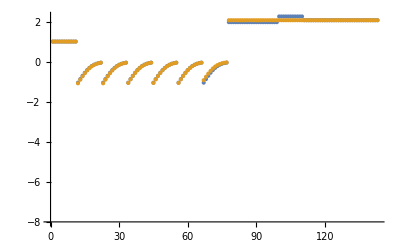

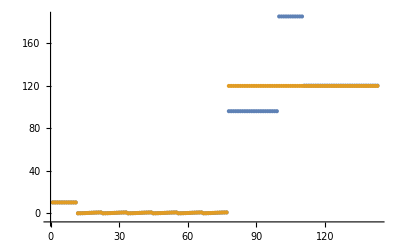

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

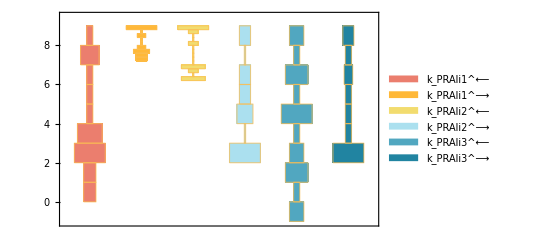

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

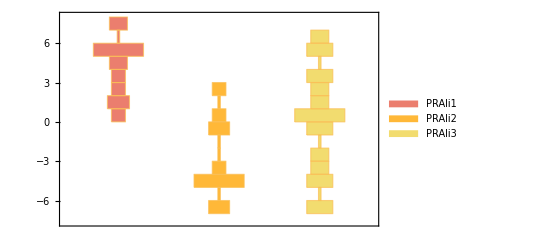

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

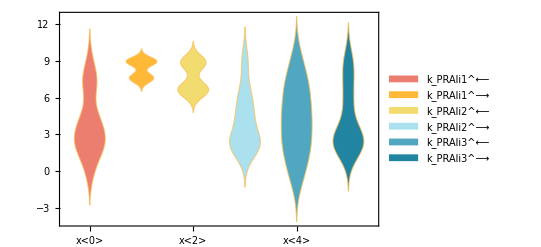

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

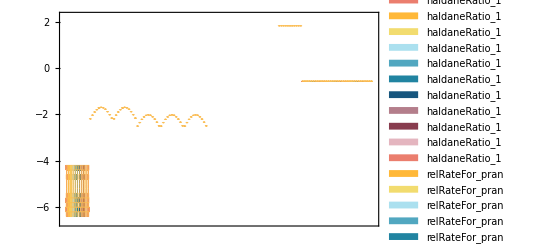

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[(pran^c⇌(2cpr5p)^c)^PRAli,{{1,pran,4.7×10^-6,{4.465×10^-6,4.935×10^-6},{},M,7.5,25,{{trishcl,0.05},{edta,0.004}},{{k,0.008},{mg2,0.004}}},{1,pran,4.7×10^-6,{4.465×10^-6,4.935×10^-6},{},M,7.5,25,{{trishcl,0.05},{edta,0.004}},{{k,0.008},{mg2,0.004}}},{1,pran,4.9×10^-6,{4.655×10^-6,5.145×10^-6},{},M,7.5,25,{{trishcl,0.05},{edta,0.004}},{{k,0.008},{mg2,0.004}}},{1,pran,4.9×10^-6,{4.655×10^-6,5.145×10^-6},{},M,7.5,25,{{trishcl,0.05},{edta,0.004}},{{k,0.008},{mg2,0.004}}},{1,pran,4.9×10^-6,{4.655×10^-6,5.145×10^-6},{},M,7.5,25,{{trishcl,0.05},{edta,0.004}},{{k,0.008},{mg2,0.004}}},{1,pran,7.×10^-6,{6.65×10^-6,7.35×10^-6},{},M,7.5,20,{{trisac,0.1}},{}}},{(pran^c k_PRAli1^⟶ (k_PRAli2^⟶+k_PRAli3^⟵+k_PRAli3^⟶))/(k_PRAli1^⟵ (k_PRAli2^⟶+k_PRAli3^⟵)+k_PRAli2^⟶ k_PRAli3^⟶+pran^c k_PRAli1^⟶ (k_PRAli2^⟶+k_PRAli3^⟵+k_PRAli3^⟶))},{((2cpr5p)^c k_PRAli2^⟵ (k_PRAli1^⟵+k_PRAli3^⟵+k_PRAli3^⟶))/(k_PRAli1^⟵ (k_PRAli2^⟶+k_PRAli3^⟵)+k_PRAli2^⟶ k_PRAli3^⟶+(2cpr5p)^c k_PRAli2^⟵ (k_PRAli1^⟵+k_PRAli3^⟵+k_PRAli3^⟶))},{pran^c→∞},{(2cpr5p)^c→∞},{k_PRAli1^⟵→7.69253×10^6,k_PRAli1^⟶→9.99999×10^8,k_PRAli2^⟵→2.34721×10^6,k_PRAli2^⟶→119.982,k_PRAli3^⟵→56026.5,k_PRAli3^⟶→8.68431×10^7},1,PRAli]

```mathematica
Print[paramFitSub]
```

{k_PRAli1^⟵→7.69253×10^6,k_PRAli1^⟶→9.99999×10^8,k_PRAli2^⟵→2.34721×10^6,k_PRAli2^⟶→119.982,k_PRAli3^⟵→56026.5,k_PRAli3^⟶→8.68431×10^7}

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
96.09 | 119.904 | 24.7828
96.09 | 119.904 | 24.7828
185.167 | 119.904 | 35.2455
120.112 | 119.904 | 0.173796
120.112 | 119.904 | 0.173796
120.112 | 119.904 | 0.173796

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
10.3 | 10.3 | 9.03876×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
10.3 | 10.3 | 9.03876×10^-6

```mathematica
{{"data value", "predicted value", "error in %"}, {12.9, 12.900000000022317, 1.7299512382469261*^-10}}
```

{{data value,predicted value,error in %},{12.9,12.9,1.72995×10^-10}}

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0.0000145,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.0909091},{1,0,0.000022981,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.136807},{1,0,0.0000364224,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.20076},{1,0,0.0000577255,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.284747},{1,0,0.0000914888,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.386863},{1,0,0.000145,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.5},{1,0,0.00022981,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.613137},{1,0,0.000364224,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.715253},{1,0,0.000577255,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.79924},{1,0,0.000914888,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.863193},{1,0,0.00145,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.909091},{1,0,0.001,1.5×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.0909091},{1,0,0.001,2.37734×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.136807},{1,0,0.001,3.76783×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.20076},{1,0,0.001,5.97161×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.284747},{1,0,0.001,9.46436×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.386863},{1,0,0.001,0.000015,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.5},{1,0,0.001,0.0000237734,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.613137},{1,0,0.001,0.0000376783,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.715253},{1,0,0.001,0.0000597161,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.79924},{1,0,0.001,0.0000946436,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.863193},{1,0,0.001,0.00015,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.909091}},{2.32837×10^-23,{0.021302,76.4848,0.000162378,0.000384575,399.883,7.02493×10^6,0.0196564,9115.38,5.44613×10^8,0.000101412},{12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091}},{Priority,6pgl[c],g6p[c],nadp[c],nadph[c],param_G6PDH2r_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.000437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.000694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.00437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.00694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.}},{1.15461×10^-22,{538.263,26248.2,1.50533×10^8,28.8607,194.069,9.19561×10^6},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.}},{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[(pran^c⇌(2cpr5p)^c)^PRAli,PRAli,«20»,{Priority,2cpr5p[c],pran[c],param_PRAli_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]